```mathematica
2+3
```

5

```mathematica
2*3
```

6

```mathematica
5/3
```

5/3

```mathematica
4/2
```

2

```mathematica
2 3
```

6

```mathematica
N[5/3,20]
```

1.6666666666666666667

```mathematica
E
```

```mathematica
ⅇ,
```

```mathematica
N[E]
```

2.71828

```mathematica
Log[10]
```

Log[10]

```mathematica
N[Log[10]]
```

2.30259

```mathematica
N[Log[E]]
```

1.

```mathematica
N[Log[10,100]]
```

2.

```mathematica
sin[Pi/2]
```

sin[π/2]

```mathematica
Sin[Pi/2]
```

1

```mathematica
Sin[Pi/4]
```

1/(√2)

```mathematica
N[Pi]
```

3.14159

```mathematica
N[Pi,20]
```

3.1415926535897932385

```mathematica
Sum[k,{k,1,m=n}]
```

1/2 n (1+n)

```mathematica
Sum[k,{k,1,n}]
```

1/2 n (1+n)

```mathematica
Sum[k,{k,1,15}]
```

120

```mathematica
Sum[k^2,{k,1,n}]
```

1/6 n (1+n) (1+2 n)

```mathematica
Sum[k^3,{k,1,n}]
```

1/4 n^2 (1+n)^2

```mathematica
Matrix[2,2]
```

Matrix[2,2]

```mathematica
A = {1,3,5}, {2,4,6},{7,8,9}
```

```mathematica
A = {A = {1,3,5}, {2,4,6},{7,8,9}}
```

{{1,3,5},{2,4,6},{7,8,9}}

```mathematica
A//MatrixForm
```

(1 | 3 | 5
2 | 4 | 6
7 | 8 | 9)

```mathematica
B = {{1,2,3},{4,5,6}}
```

{{1,2,3},{4,5,6}}

```mathematica
B//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6)

```mathematica
Det[A]
```

0

```mathematica
Inverse[A]
```

Inverse::sing: Matrix {{1, 3, 5}, {2, 4, 6}, {7, 8, 9}} is singular.

Inverse[{{1,3,5},{2,4,6},{7,8,9}}]

```mathematica
Tr[A]
```

14

```mathematica
Solve[x^2-2x+3==0,x]
```

{{x→1-ⅈ √2},{x→1+ⅈ √2}}

```mathematica
Solve[x^2+x+1==0,x]
```

{{x→-(-1)^(1/3)},{x→(-1)^(2/3)}}

```mathematica
NSolve[x^2+x+1==0,x]
```

{{x→-0.5-0.866025 ⅈ},{x→-0.5+0.866025 ⅈ}}

```mathematica
Solve[x^2+x+1===0,x]
```

```mathematica
Solve[x^2+x+1==0,x]
```

{{x→-(-1)^(1/3)},{x→(-1)^(2/3)}}

```mathematica
Factor[x^2-2x+3]
```

3-2 x+x^2

```mathematica
Factor[x^2+2x+1]
```

(1+x)^2

```mathematica
Factor[x^2+2x+3]
```

3+2 x+x^2

```mathematica
Factor[x^2+2x-3]
```

(-1+x) (3+x)

```mathematica
Factor[x^3-2x+3]
```

3-2 x+x^3

```mathematica
Factor[x^3-2x+3.0]
```

1. (1.89329+1. x) (1.58454-1.89329 x+1. x^2)

```mathematica
f[x_] := x^3+5x^2-3x+2
```

```mathematica
f[1]
```

5

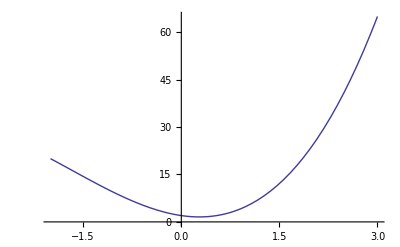

```mathematica
Plot[f[x],{x,-2,3}]
```

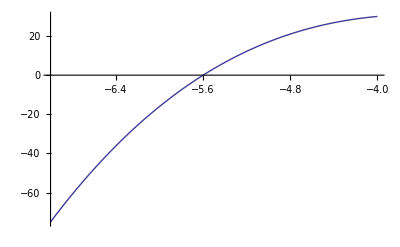

```mathematica
Plot[f[x],{x,-7,-4}]
```

```mathematica
NSolve[f[x]==0,x]
```

{{x→-5.59954},{x→0.299772-0.517019 ⅈ},{x→0.299772+0.517019 ⅈ}}

```mathematica
f[x_] := x/Sin[x]
```

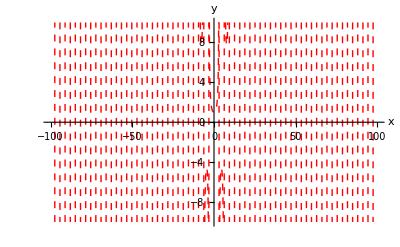

```mathematica
Plot[f[x],{x,-100,100},AxesLabel->{"x","y"},PlotRange->{-10,10},PlotStyle->{Red,Dashed}]
```

```mathematica
NSolve[f[x]== 0,x]
```

{{x→-0.5-0.866025 ⅈ},{x→-0.5+0.866025 ⅈ}}

```mathematica
Plot[f[x],{x,-200,200},AxesLabel->{"x","y"},PlotRange->{-100000,100000},PlotStyle->{Green}, AxesStyle -> Arrowheads[{-0.05,0.05}]]
```

-Graphics-

```mathematica
D[f[x],x]
```

Csc[x]-x Cot[x] Csc[x]

```mathematica
D[f[x],{x,2}]
```

-2 Cot[x] Csc[x]+x (Cot[x]^2 Csc[x]+Csc[x]^3)

```mathematica
I
```

ⅈ

```mathematica
i
```

i

```mathematica
Integrate[f[x],x]
```

x (Log[1-ⅇ^(ⅈ x)]-Log[1+ⅇ^(ⅈ x)])+ⅈ (PolyLog[2,-ⅇ^(ⅈ x)]-PolyLog[2,ⅇ^(ⅈ x)])

```mathematica
Integral[f[x],{x,-1,1}]
```

Integral[x Csc[x],{x,-1,1}]

```mathematica
Plot[Integral[f[x]],{x,-200,200}]
```

-Graphics-

```mathematica
f[x_] := x (Log[1-ⅇ^(ⅈ x)]-Log[1+ⅇ^(ⅈ x)])+ⅈ (PolyLog[2,-ⅇ^(ⅈ x)]-PolyLog[2,ⅇ^(ⅈ x)])
```

```mathematica
Plot[f[x],{x,-200,200},AxesLabel->{"x","y"},PlotRange->{-10000,10000},PlotStyle->{Green}, AxesStyle -> Arrowheads[{-0.05,0.05}]]
```

-Graphics-

```mathematica
DSolve[y'[x]+2y[x] == x,y[x],x]
```

{{y[x]→-1/4+x/2+ⅇ^(-2 x) C[1]}}

```mathematica
x^2+2x/. x-> 2
```

8

```mathematica
f[x_] := x/Sin[x]
```

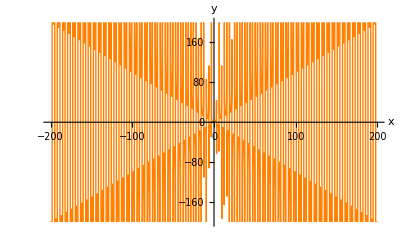

```mathematica
Plot[f[x],{x,-200,200},AxesLabel->{"x","y"},PlotRange->{-200,200},PlotStyle->{Orange}, AxesStyle -> Arrowheads[{-0.05,0.05}]]
```

```mathematica
f[x_] := √(1-(x-1)^2)
```

```mathematica
Plot[f[x],{x,-200,200},AxesLabel->{"x","y"},PlotRange->{-200,200},PlotStyle->{Orange}, AxesStyle -> Arrowheads[{-0.05,0.05}]]
```

-Graphics-

```mathematica
n=6 ;
For[ i=-24,i<6, i=i+3,
r=If[i≥0,i,-i];
Print["Absolute value of ",i," is ",r]]
Print[r]
```

Absolute value of -24 is 24

Absolute value of -21 is 21

Absolute value of -18 is 18

Absolute value of -15 is 15

Absolute value of -12 is 12

Absolute value of -9 is 9

Absolute value of -6 is 6

Absolute value of -3 is 3

Absolute value of 0 is 0

Absolute value of 3 is 3

3

```mathematica
ClearAll;
```

```mathematica
y = Input[];
Print["y = ",y];
a=If[y≥0,y,-y];
Print["Absolute Value of y is: ",a]
```

y = 5

Absolute Value of y is: 5

y = -5

Absolute Value of y is: 5

y = -5

Absolute Value of y is: 5

y = -5

```mathematica
*Bisection Method*
```

Syntax::tsntxi: "* Bisection Method *" is incomplete; more input is needed.""

Syntax::sntxi: Incomplete expression; more input is needed "".

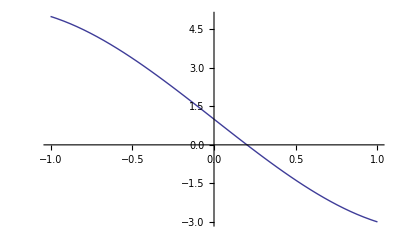

Root after iteration 1 is c= 0.5 f(c) = -1.375

Root after iteration 2 is c= 0.25 f(c) = -0.234375

Root after iteration 3 is c= 0.125 f(c) = 0.376953

Root after iteration 4 is c= 0.1875 f(c) = 0.0690918

Root after iteration 5 is c= 0.21875 f(c) = -0.0832825

Root after iteration 6 is c= 0.203125 f(c) = -0.00724411

Root after iteration 7 is c= 0.195313 f(c) = 0.0308881

Root after iteration 8 is c= 0.199219 f(c) = 0.0118129

Root after iteration 9 is c= 0.201172 f(c) = 0.00228208

Root after iteration 10 is c= 0.202148 f(c) = -0.0024816

Root after iteration 11 is c= 0.20166 f(c) = -0.0000999043

Root after iteration 12 is c= 0.201416 f(c) = 0.00109105

Root after iteration 13 is c= 0.201538 f(c) = 0.000495564

Root after iteration 14 is c= 0.201599 f(c) = 0.000197827

Root after iteration 15 is c= 0.20163 f(c) = 0.000048961

```mathematica
f[x_] := x^3-5x+1;
a=0;
b=1;
nmax=15;
Plot[f[x],{x,-1,1}]
For[i=1, i≤nmax, i++,c=(a+b)/2;
Print["Root after iteration ",i," is c= ",N[c,6]," f(c) = ",N[f[c],6],"\n"];
If[f[a]*f[c]<0,b=c,a=c];
]
```

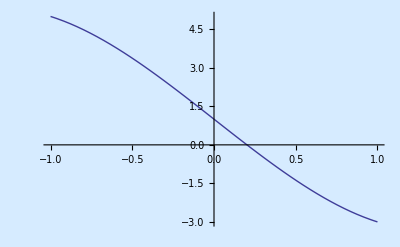

```mathematica
Show[%80,Background->RGBColor[0.84,0.92,1.]]
```

```mathematica
Show[%82,AxesStyle->Gray]
```

-Graphics-

```mathematica
f[x_] := x^3-5x+1;
a=0;
b=1;
nmax=15;
Plot[f[x],{x,-1,1}]
For[i=1,i≤nmax,i++,c=(a+b)/2;
Print[TableForm[{{i,N[c,4],N[f[c],4]}}]];
If[f[a]*f[c]<0,b=c,a=c];
]
```

-Graphics-

1 | 0.5 | -1.375

2 | 0.25 | -0.2344

3 | 0.125 | 0.377

4 | 0.1875 | 0.06909

5 | 0.2188 | -0.08328

6 | 0.2031 | -0.007244

7 | 0.1953 | 0.03089

8 | 0.1992 | 0.01181

9 | 0.2012 | 0.002282

10 | 0.2021 | -0.002482

11 | 0.2017 | -0.0000999

12 | 0.2014 | 0.001091

13 | 0.2015 | 0.0004956

14 | 0.2016 | 0.0001978

15 | 0.2016 | 0.00004896

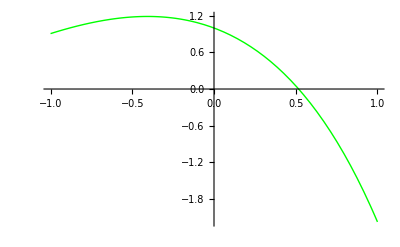

1 | 0.5 | 0.05322

2 | 0.75 | -0.8561

3 | 0.625 | -0.3567

4 | 0.5625 | -0.1413

5 | 0.5313 | -0.04151

6 | 0.5156 | 0.006475

7 | 0.5234 | -0.01736

8 | 0.5195 | -0.005404

9 | 0.5176 | 0.0005452

10 | 0.5186 | -0.002427

```mathematica
f[x_] := Cos[x]-x*E^x;
a=0;
b=1;
nmax=10;
Plot[f[x],{x,-1,1}, PlotStyle->Green]
For[i=1,i≤nmax,i++,c=(a+b)/2;
Print[TableForm[{{i,N[c,4],N[f[c],4]}}]];
If[f[a]*f[c]<0,b=c,a=c];
]
```

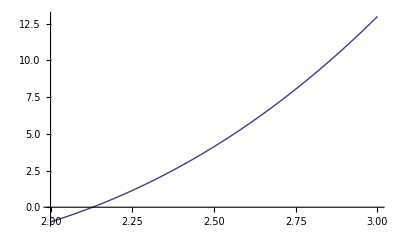

Root after iteration 1 is 2.07143

Root after iteration 2 is 2.10376

Root after iteration 3 is 2.12952

Root after iteration 4 is 2.1284

Root after iteration 5 is 2.12842

```mathematica
f[x_] := x^3-5x+1;
x0=2;
x1= 3;
nmax=5;
Plot[f[x],{x,x0,x1}]
For[i=1,i≤nmax,i++,x2=N[x1-((x1-x0)/(f[x1]-f[x0]))f[x1]];
Print["Root after iteration ",i," is ",x2];x0=x1;x1=x2;
]
```

```mathematica
*Secant Method*
```

```mathematica
f[x_] := x^3-5x+1;
x0=2;
x1= 3;
nmax=5;
Plot[f[x],{x,x0,x1}]
For[i=1,i≤nmax,i++,x2=N[x1-((x1-x0)/(f[x1]-f[x0]))f[x1]];
Print["Root after iteration ",i," is ",x2];x0=x1;x1=x2;
]
```

-Graphics-

Root after iteration 1 is 2.07143

Root after iteration 2 is 2.10376

Root after iteration 3 is 2.12952

Root after iteration 4 is 2.1284

Root after iteration 5 is 2.12842

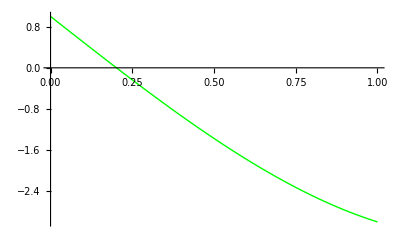

1 | 0.25 | -0.234375

2 | 0.186441 | 0.0742773

3 | 0.201736 | -0.000471116

4 | 0.20164 | -8.64229×10^-7

5 | 0.20164 | 1.03527×10^-11

6 | 0.20164 | -2.22045×10^-16

7 | 0.20164 | 1.11022×10^-16

8 | 0.20164 | 1.11022×10^-16

```mathematica
f[x_] := x^3-5x+1;
x0=0;
x1= 1;
nmax=8;
Plot[f[x],{x,x0,x1},PlotStyle->Green]
For[i=1,i≤nmax,i++,x2=N[x1-((x1-x0)/(f[x1]-f[x0]))f[x1]];
Print[TableForm[{{i,N[x2],N[f[x2]]}}]];x0=x1;x1=x2;
]
```